## SE 267A HW1

## Problem 1

```mathematica
(* Define each harmonic signal. *)
f1[t_] = Cos[(2000π)t];
f2[t_] = 5Sin[(6000π)t];
f3[t_] = 10Cos[(12000π)t];
f4[t_] = 20Cos[(15000π)t];
f5[t_] = 10Sin[(20000π)t];

(* Sum up all the harmonics to get the original analog signal. *)
Print[Style["Original analog signal: ", Bold, FontFamily->"Times", FontSize->14],
	Style["f(t)", Italic, Bold, FontFamily->"Times", FontSize->14]]
f[t_] = f1[t]+f2[t]+f3[t]+f4[t]+f5[t]

(* Plot the original analog signal. *)
Plot[{f[t]}, {t, -0.002, 0.002}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.005]},
	PlotLegends->{Style["Original Analog Signal"]}, FrameLabel->{Style["t", Italic], Style["f(t)", Italic]},
	PlotLabel->"Original Analog Signal", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold,
	FontSize->14, FontFamily->"Times"}, Frame->True]
	
(* Plot each harmonic signal separately. *)
Plot[{f1[t], f2[t], f3[t], f4[t], f5[t]}, {t, -0.002, 0.002}, ImageSize->{400, 300},
	PlotStyle->{Blue, Red, Green, Orange, Black}, PlotLegends->{Style[Subscript["f", 1][t],
	Italic], Style[Subscript["f", 2][t], Italic], Style[Subscript["f", 3][t], Italic],
	Style[Subscript["f", 4][t], Italic], Style[Subscript["f", 5][t], Italic]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Harmonic Signals",
	GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"},
	Frame->True]
```

Original analog signal: f(t)

Cos[2000 π t]+10 Cos[12000 π t]+20 Cos[15000 π t]+5 Sin[6000 π t]+10 Sin[20000 π t]

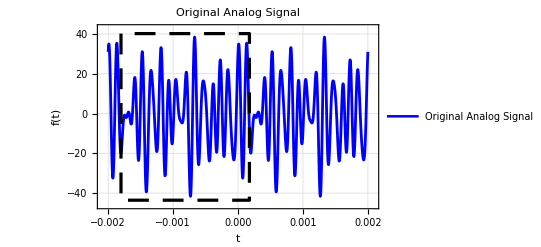

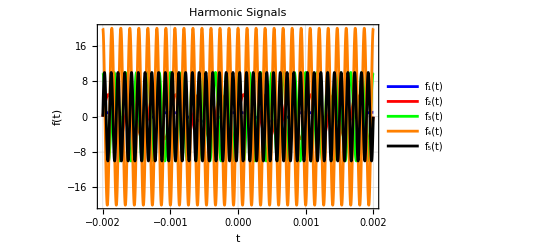

There are 5 distinct frequencies composing the signal.

By visual inspection, the fundamental period of the signal is T_p = 0.002 s.
The full cycle of the signal is marked with black dash lines in the plot.

## Problem 2

```mathematica
(* Define each harmonic signal in the cosine function form. *)
Index = {1, 2, 3, 4, 5}; 

Print[Style["Angular frequency Ω_i (rad/s) for each harmonic signal:", Bold, FontFamily->"Times", FontSize->14]]
Omega = {2000π, 6000π, 12000π, 15000π, 20000π}

Print[Style["Fundamental frequency f_pi (Hz) for each harmonic signal:", Bold, FontFamily->"Times", FontSize->14]]
Frequency = Omega/(2π)

Print[Style["Fundamental period T_pi (s) for each harmonic signal:", Bold, FontFamily->"Times", FontSize->14]]
Period = 1/Frequency

Print[Style["Amplitude A_i for each harmonic signal:", Bold, FontFamily->"Times", FontSize->14]]
Amplitude = {1, 5, 10, 20, 10}

Print[Style["Phase difference Φ_i (rad) for each harmonic signal:", Bold, FontFamily->"Times", FontSize->14]]
Phi = {0, -π/2, 0, 0, -π/2}

f1[t_] = Amplitude[[1]] * Cos[Omega[[1]]*t + Phi[[1]]];
f2[t_] = Amplitude[[2]] * Cos[Omega[[2]]*t + Phi[[2]]];
f3[t_] = Amplitude[[3]] * Cos[Omega[[3]]*t + Phi[[3]]];
f4[t_] = Amplitude[[4]] * Cos[Omega[[4]]*t + Phi[[4]]];
f5[t_] = Amplitude[[5]] * Cos[Omega[[5]]*t + Phi[[5]]];

(* List a table for the characteristics of harmonics. *)
Title = {"Harmonic index i", "Angular frequency Ω_i (rad/s)", "Fundamental frequency f_pi (Hz)",
	"Fundamental period T_pi (s)", "Amplitude A_i", "Phase difference Φ_i (rad)"};
Data = Transpose[{Index, Omega, Frequency, Period, Amplitude, Phi}];
AppendData = Prepend[Data, Title];
StyledData = Map[Style[#, FontFamily->"Times", FontSize->10, FontWeight->Bold] &, AppendData, {2}];
Grid[StyledData, Frame->All, ItemSize->{8, 2}, Alignment->Center]

(* Sum up all the harmonics to get the original analog signal. *)
f[t_] = f1[t]+f2[t]+f3[t]+f4[t]+f5[t];

(* Print all the harmonics and the original analog signal. *)
Print[Style["Harmonic signal: ", Bold, FontFamily->"Times", FontSize->14],
	Style["f_1(t)", Italic, Bold, FontFamily->"Times", FontSize->14]]
f1[t]/.Sin[var_]:>HoldForm[Cos[var-π/2]]

Print[Style["Harmonic signal: ", Bold, FontFamily->"Times", FontSize->14],
	Style["f_2(t)", Italic, Bold, FontFamily->"Times", FontSize->14]]
f2[t]/.Sin[var_]:>HoldForm[Cos[var-π/2]]

Print[Style["Harmonic signal: ", Bold, FontFamily->"Times", FontSize->14],
	Style["f_3(t)", Italic, Bold, FontFamily->"Times", FontSize->14]]
f3[t]/.Sin[var_]:>HoldForm[Cos[var-π/2]]

Print[Style["Harmonic signal: ", Bold, FontFamily->"Times", FontSize->14],
	Style["f_4(t)", Italic, Bold, FontFamily->"Times", FontSize->14]]
f4[t]/.Sin[var_]:>HoldForm[Cos[var-π/2]]

Print[Style["Harmonic signal: ", Bold, FontFamily->"Times", FontSize->14],
	Style["f_5(t)", Italic, Bold, FontFamily->"Times", FontSize->14]]
f5[t]/.Sin[var_]:>HoldForm[Cos[var-π/2]]

Print[Style["Original analog signal: ", Bold, FontFamily->"Times", FontSize->14],
	Style["f(t)", Italic, Bold, FontFamily->"Times", FontSize->14]]
f[t]/.Sin[var_]:>HoldForm[Cos[var-π/2]]
```

Angular frequency Ω_i (rad/s) for each harmonic signal:

{2000 π,6000 π,12000 π,15000 π,20000 π}

Fundamental frequency f_pi (Hz) for each harmonic signal:

{1000,3000,6000,7500,10000}

Fundamental period T_pi (s) for each harmonic signal:

{1/1000,1/3000,1/6000,1/7500,1/10000}

Amplitude A_i for each harmonic signal:

{1,5,10,20,10}

Phase difference Φ_i (rad) for each harmonic signal:

{0,-π/2,0,0,-π/2}

Harmonic index i | Angular frequency Ω_i (rad/s) | Fundamental frequency f_pi (Hz) | Fundamental period T_pi (s) | Amplitude A_i | Phase difference Φ_i (rad)
1 | 2000 π | 1000 | 1/1000 | 1 | 0
2 | 6000 π | 3000 | 1/3000 | 5 | -π/2
3 | 12000 π | 6000 | 1/6000 | 10 | 0
4 | 15000 π | 7500 | 1/7500 | 20 | 0
5 | 20000 π | 10000 | 1/10000 | 10 | -π/2

Harmonic signal: f_1(t)

Cos[2000 π t]

Harmonic signal: f_2(t)

5 Cos[6000 π t-π/2]

Harmonic signal: f_3(t)

10 Cos[12000 π t]

Harmonic signal: f_4(t)

20 Cos[15000 π t]

Harmonic signal: f_5(t)

10 Cos[20000 π t-π/2]

Original analog signal: f(t)

Cos[2000 π t]+10 Cos[12000 π t]+20 Cos[15000 π t]+5 Cos[6000 π t-π/2]+10 Cos[20000 π t-π/2]

## Problem 3

```mathematica
(* Calculate the fundamental time period of the original analog signal. *)
Print[Style["The fundamental time period T_p (second) of the original analog signal:", Bold,
	FontFamily->"Times", FontSize->14]]
Tp = LCM[Period[[1]], Period[[2]], Period[[3]], Period[[4]], Period[[5]]]
```

The fundamental time period T_p (second) of the original analog signal:

1/500

The fundamental time period of signal is f(t) = 0.002 s, which can match the result from visual inspection.

## Problem 4

```mathematica
(* Calculate the fundamental frequency and angular frequency. *)
Print[Style["The fundamental frequency f_p (Hz) of the original analog signal:", Bold,
	FontFamily->"Times", FontSize->14]]
Analogfp = 1/Tp

Print[Style["The angular frequency Ω (rad/s) of the original analog signal:", Bold,
	FontFamily->"Times", FontSize->14]]
AnalogOmega = 2π*Analogfp
```

The fundamental frequency f_p (Hz) of the original analog signal:

500

The angular frequency Ω (rad/s) of the original analog signal:

1000 π

## Problem 5

```mathematica
(* Obtain the maximum frequency of the original analog signal. *)
Print[Style["The maximum frequency f_(p, max) (Hz) of the original analog signal:", Bold,
	FontFamily->"Times", FontSize->14]]
MaxFrequency = Max[Frequency]

(* Calculate the Nyquist frequency of the original analog signal. *)
Print[Style["The Nyquist frequency f_N (Hz) of the original analog signal:", Bold,
	FontFamily->"Times", FontSize->14]]
NyquistFrequency = 2*MaxFrequency
```

The maximum frequency f_(p, max) (Hz) of the original analog signal:

10000

The Nyquist frequency f_N (Hz) of the original analog signal:

20000

## Problem 6

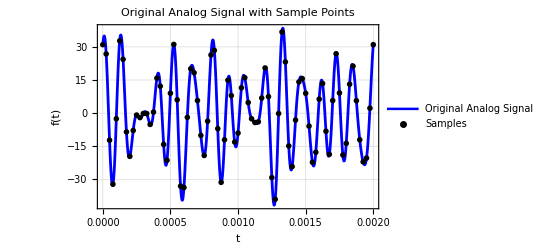

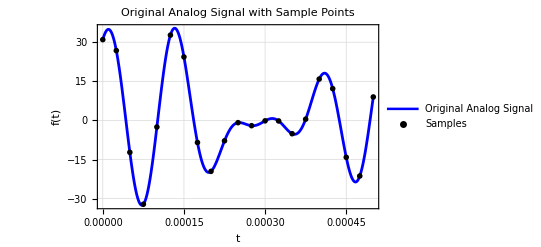

```mathematica
(* Given the sampling frequency equal to two times the Nyquist frequency. *)
SamplingFrequency = 2 * NyquistFrequency;
SamplingTime = Range[0, 0.002, 1/SamplingFrequency];

(* Sample the signal. *)
fSeq = Table[N[f[SamplingTime[[k]]]], {k, 1, Length[SamplingTime]}];
fSeqList = Transpose[{SamplingTime, fSeq}];

(* Plot the original signal and the sampled signal. *)
Show[Plot[f[t], {t, 0, 0.002}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.005]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]},
	PlotLabel->"Original Analog Signal with Sample Points", GridLines->Automatic,
	LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
ListPlot[fSeqList, PlotStyle->{Directive[PointSize[0.01], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}]]
	
Show[Plot[f[t], {t, 0, 0.0005}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.005]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]},
	PlotLabel->"Original Analog Signal with Sample Points", GridLines->Automatic,
	LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
ListPlot[fSeqList, PlotStyle->{Directive[PointSize[0.01], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}]]
```

## Problem 7

```mathematica
(* Calculate Subscript[ω, i] for each harmonic signal. *)
Print[Style["ω_i (rad/sample) for each harmonic signal:", Bold,
	FontFamily->"Times", FontSize->14]]
w = Omega/SamplingFrequency

(* Calculate the analytical form of the discrete-time signal after sampling. *)
fSeqAnalytical[n_] = Total[Amplitude * Cos[w*n + Phi]];

Print[Style["Discrete-time signal: ", Bold, FontFamily->"Times", FontSize->14],
	Style["f(n)", Italic, Bold, FontFamily->"Times", FontSize->14]]
fSeqAnalytical[n]/.Sin[var_]:>HoldForm[Cos[var-π/2]]
```

ω_i (rad/sample) for each harmonic signal:

{π/20,(3 π)/20,(3 π)/10,(3 π)/8,π/2}

Discrete-time signal: f(n)

Cos[(n π)/20]+10 Cos[(3 n π)/10]+20 Cos[(3 n π)/8]+5 Cos[(3 n π)/20-π/2]+10 Cos[(n π)/2-π/2]

## Problem 8

See the handwritten pages at the end.

## Problem 9

```mathematica
(* Calculate the frequency, amplitude and phase difference values. *)
MirrorFrequency = SamplingFrequency - Frequency;
MirrorAmplitude = Amplitude;
MirrorPhi = -Phi;
MirrorOmega = 2π * MirrorFrequency;
MirrorW = MirrorOmega/SamplingFrequency;

CopyFrequency = SamplingFrequency + Frequency;
CopyAmplitude = Amplitude;
CopyPhi = Phi;
CopyOmega = 2π * CopyFrequency;
CopyW = CopyOmega/SamplingFrequency;

(* Discrete-time signal for the 1st mirror alias. *)
fSeqMirror[n_] = Total[MirrorAmplitude * Cos[MirrorW*n + MirrorPhi]];
Print[Style["Discrete-time signal for the 1st mirror alias: ", Bold, FontFamily->"Times", FontSize->14]]
TraditionalForm[fSeqMirror[n]/.Sin[var_]:>HoldForm[Cos[var-π/2]]]

(* Discrete-time signal for the 1st copy alias. *)
fSeqCopy[n_] = Total[CopyAmplitude * Cos[CopyW*n + CopyPhi]];
Print[Style["Discrete-time signal for the 1st copy alias: ", Bold, FontFamily->"Times", FontSize->14]]
TraditionalForm[fSeqCopy[n]/.Sin[var_]:>HoldForm[Cos[var-π/2]]]

(* Analog signal for the 1st mirror alias. *)
fMirror[t_] = Total[MirrorAmplitude * Cos[MirrorOmega*t + MirrorPhi]];
Print[Style["Analog signal for the 1st mirror alias: ", Bold, FontFamily->"Times", FontSize->14]]
TraditionalForm[fMirror[t]/.Sin[var_]:>HoldForm[Cos[var-π/2]]]

(* Analog signal for the 1st copy alias. *)
fCopy[t_] = Total[CopyAmplitude * Cos[CopyOmega*t + CopyPhi]];
Print[Style["Analog signal for the 1st copy alias: ", Bold, FontFamily->"Times", FontSize->14]]
TraditionalForm[fCopy[t]/.Sin[var_]:>HoldForm[Cos[var-π/2]]]
```

Discrete-time signal for the 1st mirror alias:

20 cos((13 π n)/8)+10 cos((17 π n)/10)+cos((39 π n)/20)-10 cos((3 n π)/2-π/2)-5 cos((37 n π)/20-π/2)

Discrete-time signal for the 1st copy alias:

cos((41 π n)/20)+10 cos((23 π n)/10)+20 cos((19 π n)/8)+5 cos((43 n π)/20-π/2)+10 cos((5 n π)/2-π/2)

Analog signal for the 1st mirror alias:

20 cos(65000 π t)+10 cos(68000 π t)+cos(78000 π t)-10 cos(60000 π t-π/2)-5 cos(74000 π t-π/2)

Analog signal for the 1st copy alias:

cos(82000 π t)+10 cos(92000 π t)+20 cos(95000 π t)+5 cos(86000 π t-π/2)+10 cos(100000 π t-π/2)

## Problem 10

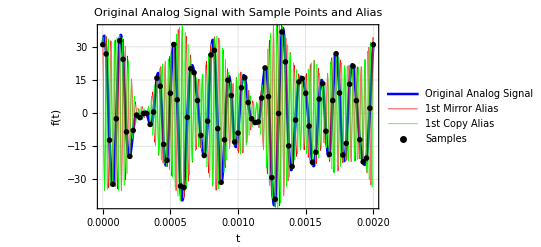

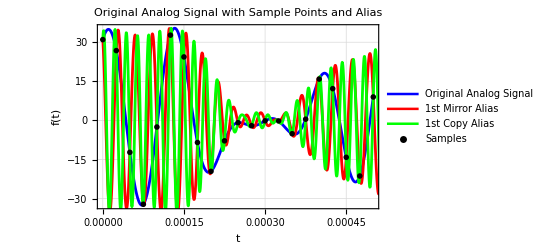

```mathematica
(* Plot the original signal, the sampled signal and the alias. *)
Show[Plot[f[t], {t, 0, 0.002}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.005]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]},
	PlotLabel->"Original Analog Signal with Sample Points and Alias", GridLines->Automatic,
	LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
Plot[fMirror[t], {t, 0, 0.002}, PlotStyle->{Red, Thickness[0.001]},
	PlotLegends->{Style["1st Mirror Alias", Bold, FontSize->14, FontFamily->"Times"]}],
Plot[fCopy[t], {t, 0, 0.002}, PlotStyle->{Green, Thickness[0.001]},
	PlotLegends->{Style["1st Copy Alias", Bold, FontSize->14, FontFamily->"Times"]}],
ListPlot[fSeqList, PlotStyle->{Directive[PointSize[0.01], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}]]
	
Show[Plot[f[t], {t, 0, 0.0005}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.005]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]},
	PlotLabel->"Original Analog Signal with Sample Points and Alias", GridLines->Automatic,
	LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
Plot[fMirror[t], {t, 0, 0.002}, PlotStyle->{Red, Thickness[0.005]},
	PlotLegends->{Style["1st Mirror Alias", Bold, FontSize->14, FontFamily->"Times"]}],
Plot[fCopy[t], {t, 0, 0.002}, PlotStyle->{Green, Thickness[0.005]},
	PlotLegends->{Style["1st Copy Alias", Bold, FontSize->14, FontFamily->"Times"]}],
ListPlot[fSeqList, PlotStyle->{Directive[PointSize[0.01], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}]]
```

## Problem 11

The set of shape functions:

{(7.95775×10^-6 sin(125664. t))/t,(7.95775×10^-6 sin(125664. (t-0.000025)))/(t-0.000025),(7.95775×10^-6 sin(125664. (t-0.00005)))/(t-0.00005),(7.95775×10^-6 sin(125664. (t-0.000075)))/(t-0.000075),(7.95775×10^-6 sin(125664. (t-0.0001)))/(t-0.0001),(7.95775×10^-6 sin(125664. (t-0.000125)))/(t-0.000125),(7.95775×10^-6 sin(125664. (t-0.00015)))/(t-0.00015),(7.95775×10^-6 sin(125664. (t-0.000175)))/(t-0.000175),(7.95775×10^-6 sin(125664. (t-0.0002)))/(t-0.0002),(7.95775×10^-6 sin(125664. (t-0.000225)))/(t-0.000225),(7.95775×10^-6 sin(125664. (t-0.00025)))/(t-0.00025),(7.95775×10^-6 sin(125664. (t-0.000275)))/(t-0.000275),(7.95775×10^-6 sin(125664. (t-0.0003)))/(t-0.0003),(7.95775×10^-6 sin(125664. (t-0.000325)))/(t-0.000325),(7.95775×10^-6 sin(125664. (t-0.00035)))/(t-0.00035),(7.95775×10^-6 sin(125664. (t-0.000375)))/(t-0.000375),(7.95775×10^-6 sin(125664. (t-0.0004)))/(t-0.0004),(7.95775×10^-6 sin(125664. (t-0.000425)))/(t-0.000425),(7.95775×10^-6 sin(125664. (t-0.00045)))/(t-0.00045),(7.95775×10^-6 sin(125664. (t-0.000475)))/(t-0.000475),(7.95775×10^-6 sin(125664. (t-0.0005)))/(t-0.0005),(7.95775×10^-6 sin(125664. (t-0.000525)))/(t-0.000525),(7.95775×10^-6 sin(125664. (t-0.00055)))/(t-0.00055),(7.95775×10^-6 sin(125664. (t-0.000575)))/(t-0.000575),(7.95775×10^-6 sin(125664. (t-0.0006)))/(t-0.0006),(7.95775×10^-6 sin(125664. (t-0.000625)))/(t-0.000625),(7.95775×10^-6 sin(125664. (t-0.00065)))/(t-0.00065),(7.95775×10^-6 sin(125664. (t-0.000675)))/(t-0.000675),(7.95775×10^-6 sin(125664. (t-0.0007)))/(t-0.0007),(7.95775×10^-6 sin(125664. (t-0.000725)))/(t-0.000725),(7.95775×10^-6 sin(125664. (t-0.00075)))/(t-0.00075),(7.95775×10^-6 sin(125664. (t-0.000775)))/(t-0.000775),(7.95775×10^-6 sin(125664. (t-0.0008)))/(t-0.0008),(7.95775×10^-6 sin(125664. (t-0.000825)))/(t-0.000825),(7.95775×10^-6 sin(125664. (t-0.00085)))/(t-0.00085),(7.95775×10^-6 sin(125664. (t-0.000875)))/(t-0.000875),(7.95775×10^-6 sin(125664. (t-0.0009)))/(t-0.0009),(7.95775×10^-6 sin(125664. (t-0.000925)))/(t-0.000925),(7.95775×10^-6 sin(125664. (t-0.00095)))/(t-0.00095),(7.95775×10^-6 sin(125664. (t-0.000975)))/(t-0.000975),(7.95775×10^-6 sin(125664. (t-0.001)))/(t-0.001),(7.95775×10^-6 sin(125664. (t-0.001025)))/(t-0.001025),(7.95775×10^-6 sin(125664. (t-0.00105)))/(t-0.00105),(7.95775×10^-6 sin(125664. (t-0.001075)))/(t-0.001075),(7.95775×10^-6 sin(125664. (t-0.0011)))/(t-0.0011),(7.95775×10^-6 sin(125664. (t-0.001125)))/(t-0.001125),(7.95775×10^-6 sin(125664. (t-0.00115)))/(t-0.00115),(7.95775×10^-6 sin(125664. (t-0.001175)))/(t-0.001175),(7.95775×10^-6 sin(125664. (t-0.0012)))/(t-0.0012),(7.95775×10^-6 sin(125664. (t-0.001225)))/(t-0.001225),(7.95775×10^-6 sin(125664. (t-0.00125)))/(t-0.00125),(7.95775×10^-6 sin(125664. (t-0.001275)))/(t-0.001275),(7.95775×10^-6 sin(125664. (t-0.0013)))/(t-0.0013),(7.95775×10^-6 sin(125664. (t-0.001325)))/(t-0.001325),(7.95775×10^-6 sin(125664. (t-0.00135)))/(t-0.00135),(7.95775×10^-6 sin(125664. (t-0.001375)))/(t-0.001375),(7.95775×10^-6 sin(125664. (t-0.0014)))/(t-0.0014),(7.95775×10^-6 sin(125664. (t-0.001425)))/(t-0.001425),(7.95775×10^-6 sin(125664. (t-0.00145)))/(t-0.00145),(7.95775×10^-6 sin(125664. (t-0.001475)))/(t-0.001475),(7.95775×10^-6 sin(125664. (t-0.0015)))/(t-0.0015),(7.95775×10^-6 sin(125664. (t-0.001525)))/(t-0.001525),(7.95775×10^-6 sin(125664. (t-0.00155)))/(t-0.00155),(7.95775×10^-6 sin(125664. (t-0.001575)))/(t-0.001575),(7.95775×10^-6 sin(125664. (t-0.0016)))/(t-0.0016),(7.95775×10^-6 sin(125664. (t-0.001625)))/(t-0.001625),(7.95775×10^-6 sin(125664. (t-0.00165)))/(t-0.00165),(7.95775×10^-6 sin(125664. (t-0.001675)))/(t-0.001675),(7.95775×10^-6 sin(125664. (t-0.0017)))/(t-0.0017),(7.95775×10^-6 sin(125664. (t-0.001725)))/(t-0.001725),(7.95775×10^-6 sin(125664. (t-0.00175)))/(t-0.00175),(7.95775×10^-6 sin(125664. (t-0.001775)))/(t-0.001775),(7.95775×10^-6 sin(125664. (t-0.0018)))/(t-0.0018),(7.95775×10^-6 sin(125664. (t-0.001825)))/(t-0.001825),(7.95775×10^-6 sin(125664. (t-0.00185)))/(t-0.00185),(7.95775×10^-6 sin(125664. (t-0.001875)))/(t-0.001875),(7.95775×10^-6 sin(125664. (t-0.0019)))/(t-0.0019),(7.95775×10^-6 sin(125664. (t-0.001925)))/(t-0.001925),(7.95775×10^-6 sin(125664. (t-0.00195)))/(t-0.00195),(7.95775×10^-6 sin(125664. (t-0.001975)))/(t-0.001975),(7.95775×10^-6 sin(125664. (t-0.002)))/(t-0.002)}

The reconstructed signal using samples:

(0.00024669 sin(125664. (t-0.002)))/(t-0.002)+(0.000017899 sin(125664. (t-0.001975)))/(t-0.001975)-(0.000161752 sin(125664. (t-0.00195)))/(t-0.00195)-(0.000175354 sin(125664. (t-0.001925)))/(t-0.001925)-(0.0000957829 sin(125664. (t-0.0019)))/(t-0.0019)+(0.0000449546 sin(125664. (t-0.001875)))/(t-0.001875)+(0.000169301 sin(125664. (t-0.00185)))/(t-0.00185)+(0.000104191 sin(125664. (t-0.001825)))/(t-0.001825)-(0.000108718 sin(125664. (t-0.0018)))/(t-0.0018)-(0.000150561 sin(125664. (t-0.001775)))/(t-0.001775)+(0.0000727508 sin(125664. (t-0.00175)))/(t-0.00175)+(0.00021405 sin(125664. (t-0.001725)))/(t-0.001725)+(0.0000455189 sin(125664. (t-0.0017)))/(t-0.0017)-(0.000148323 sin(125664. (t-0.001675)))/(t-0.001675)-(0.0000651329 sin(125664. (t-0.00165)))/(t-0.00165)+(0.000106722 sin(125664. (t-0.001625)))/(t-0.001625)+(0.0000504961 sin(125664. (t-0.0016)))/(t-0.0016)-(0.000140743 sin(125664. (t-0.001575)))/(t-0.001575)-(0.000176888 sin(125664. (t-0.00155)))/(t-0.00155)-(0.0000466115 sin(125664. (t-0.001525)))/(t-0.001525)+(0.0000716197 sin(125664. (t-0.0015)))/(t-0.0015)+(0.000124441 sin(125664. (t-0.001475)))/(t-0.001475)+(0.00011257 sin(125664. (t-0.00145)))/(t-0.00145)-(0.0000248027 sin(125664. (t-0.001425)))/(t-0.001425)-(0.000192131 sin(125664. (t-0.0014)))/(t-0.0014)-(0.000117976 sin(125664. (t-0.001375)))/(t-0.001375)+(0.000184537 sin(125664. (t-0.00135)))/(t-0.00135)+(0.000292463 sin(125664. (t-0.001325)))/(t-0.001325)-(1.25552×10^-6 sin(125664. (t-0.0013)))/(t-0.0013)-(0.000310089 sin(125664. (t-0.001275)))/(t-0.001275)-(0.000231906 sin(125664. (t-0.00125)))/(t-0.00125)+(0.0000595018 sin(125664. (t-0.001225)))/(t-0.001225)+(0.000162818 sin(125664. (t-0.0012)))/(t-0.0012)+(0.0000543996 sin(125664. (t-0.001175)))/(t-0.001175)-(0.0000311872 sin(125664. (t-0.00115)))/(t-0.00115)-(0.0000337007 sin(125664. (t-0.001125)))/(t-0.001125)-(0.0000201002 sin(125664. (t-0.0011)))/(t-0.0011)+(0.0000381691 sin(125664. (t-0.001075)))/(t-0.001075)+(0.000127707 sin(125664. (t-0.00105)))/(t-0.00105)+(0.0000913695 sin(125664. (t-0.001025)))/(t-0.001025)-(0.0000716197 sin(125664. (t-0.001)))/(t-0.001)-(0.000103913 sin(125664. (t-0.000975)))/(t-0.000975)+(0.0000633273 sin(125664. (t-0.00095)))/(t-0.00095)+(0.000118726 sin(125664. (t-0.000925)))/(t-0.000925)-(0.0000957829 sin(125664. (t-0.0009)))/(t-0.0009)-(0.000249125 sin(125664. (t-0.000875)))/(t-0.000875)-(0.000055778 sin(125664. (t-0.00085)))/(t-0.00085)+(0.000226003 sin(125664. (t-0.000825)))/(t-0.000825)+(0.000209592 sin(125664. (t-0.0008)))/(t-0.0008)-(0.0000287491 sin(125664. (t-0.000775)))/(t-0.000775)-(0.000152328 sin(125664. (t-0.00075)))/(t-0.00075)-(0.0000800298 sin(125664. (t-0.000725)))/(t-0.000725)+(0.0000455189 sin(125664. (t-0.0007)))/(t-0.0007)+(0.000145757 sin(125664. (t-0.000675)))/(t-0.000675)+(0.000159946 sin(125664. (t-0.00065)))/(t-0.00065)-(0.0000150904 sin(125664. (t-0.000625)))/(t-0.000625)-(0.000267814 sin(125664. (t-0.0006)))/(t-0.0006)-(0.000262555 sin(125664. (t-0.000575)))/(t-0.000575)+(0.0000481907 sin(125664. (t-0.00055)))/(t-0.00055)+(0.000247468 sin(125664. (t-0.000525)))/(t-0.000525)+(0.0000716197 sin(125664. (t-0.0005)))/(t-0.0005)-(0.000169639 sin(125664. (t-0.000475)))/(t-0.000475)-(0.000112509 sin(125664. (t-0.00045)))/(t-0.00045)+(0.0000970092 sin(125664. (t-0.000425)))/(t-0.000425)+(0.000126179 sin(125664. (t-0.0004)))/(t-0.0004)+(3.8364×10^-6 sin(125664. (t-0.000375)))/(t-0.000375)-(0.0000405421 sin(125664. (t-0.00035)))/(t-0.00035)-(1.61692×10^-6 sin(125664. (t-0.000325)))/(t-0.000325)-(1.25552×10^-6 sin(125664. (t-0.0003)))/(t-0.0003)-(0.0000160088 sin(125664. (t-0.000275)))/(t-0.000275)-(6.82667×10^-6 sin(125664. (t-0.00025)))/(t-0.00025)-(0.0000623101 sin(125664. (t-0.000225)))/(t-0.000225)-(0.000155492 sin(125664. (t-0.0002)))/(t-0.0002)-(0.0000674123 sin(125664. (t-0.000175)))/(t-0.000175)+(0.000193892 sin(125664. (t-0.00015)))/(t-0.00015)+(0.000260379 sin(125664. (t-0.000125)))/(t-0.000125)-(0.0000201002 sin(125664. (t-0.0001)))/(t-0.0001)-(0.000255911 sin(125664. (t-0.000075)))/(t-0.000075)-(0.0000973723 sin(125664. (t-0.00005)))/(t-0.00005)+(0.000213181 sin(125664. (t-0.000025)))/(t-0.000025)+(0.00024669 sin(125664. t))/t

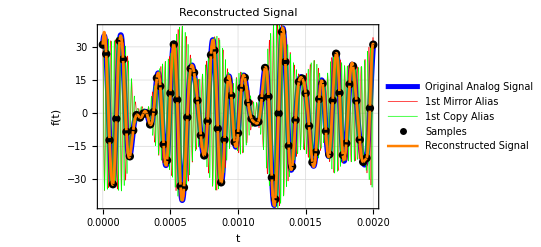

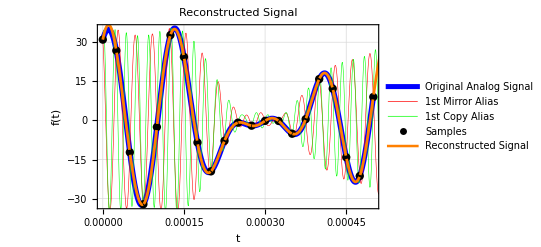

```mathematica
(* Define the set of shape functions. *)
ShapeFunctionSet = N[Table[Sin[2π*(SamplingFrequency/2)*(t-n/SamplingFrequency)] / (2π*(SamplingFrequency/2)*(t-n/SamplingFrequency)),
	{n, 0, Length[SamplingTime]-1}]];
Print[Style["The set of shape functions: ", Bold, FontFamily->"Times", FontSize->14]]
TraditionalForm[ShapeFunctionSet]

(* Reconstruct the signal using the samples. *)
ReconstructedSignal = Dot[fSeq, ShapeFunctionSet];
Print[Style["The reconstructed signal using samples: ", Bold, FontFamily->"Times", FontSize->14]]
TraditionalForm[ReconstructedSignal]

(* Plot the reconstructed signal with the original signal and its alias. *)
Show[Plot[f[t], {t, 0, 0.002}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.01]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Reconstructed Signal",
	GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
Plot[fMirror[t], {t, 0, 0.002}, PlotStyle->{Red, Thickness[0.001]},
	PlotLegends->{Style["1st Mirror Alias", Bold, FontSize->14, FontFamily->"Times"]}],
Plot[fCopy[t], {t, 0, 0.002}, PlotStyle->{Green, Thickness[0.001]},
	PlotLegends->{Style["1st Copy Alias", Bold, FontSize->14, FontFamily->"Times"]}],
ListPlot[fSeqList, PlotStyle->{Directive[PointSize[0.015], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}],
Plot[ReconstructedSignal, {t, 0, 0.002}, PlotStyle->{Orange, Thickness[0.005]},
	PlotLegends->{Style["Reconstructed Signal", Bold, FontSize->14, FontFamily->"Times"]}]]

Show[Plot[f[t], {t, 0, 0.0005}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.01]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Reconstructed Signal",
	GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
Plot[fMirror[t], {t, 0, 0.002}, PlotStyle->{Red, Thickness[0.001]},
	PlotLegends->{Style["1st Mirror Alias", Bold, FontSize->14, FontFamily->"Times"]}],
Plot[fCopy[t], {t, 0, 0.002}, PlotStyle->{Green, Thickness[0.001]},
	PlotLegends->{Style["1st Copy Alias", Bold, FontSize->14, FontFamily->"Times"]}],
ListPlot[fSeqList, PlotStyle->{Directive[PointSize[0.015], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}],
Plot[ReconstructedSignal, {t, 0, 0.002}, PlotStyle->{Orange, Thickness[0.005]},
	PlotLegends->{Style["Reconstructed Signal", Bold, FontSize->14, FontFamily->"Times"]}]]
```

## Problem 12

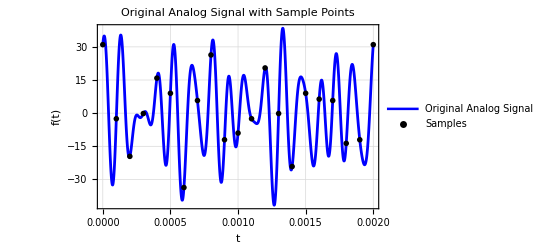

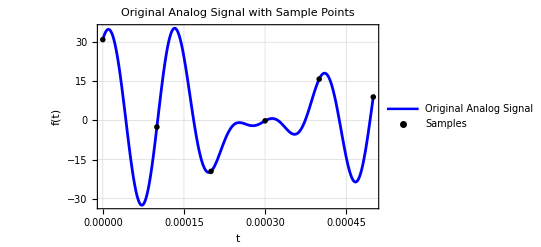

```mathematica
(* Given the sampling frequency is the half of the Nyquist frequency. *)
SamplingFrequency2 = NyquistFrequency/2;
SamplingTime2 = Range[0, 0.002, 1/SamplingFrequency2];

(* Sample the signal. *)
fSeq2 = Table[N[f[SamplingTime2[[i]]]], {i, 1, Length[SamplingTime2]}];
fSeqList2 = Transpose[{SamplingTime2, fSeq2}];

(* Plot the original signal and the sampled signal. *)
Show[Plot[{f[t]}, {t, 0, 0.002}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.005]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]},
	PlotLabel->"Original Analog Signal with Sample Points", GridLines->Automatic,
	LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
ListPlot[fSeqList2, PlotStyle->{Directive[PointSize[0.01], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}]]
	
Show[Plot[{f[t]}, {t, 0, 0.0005}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.005]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]},
	PlotLabel->"Original Analog Signal with Sample Points", GridLines->Automatic,
	LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
ListPlot[fSeqList2, PlotStyle->{Directive[PointSize[0.01], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}]]
```

## Problem 13

The set of shape functions:

{(7.95775×10^-6 sin(125664. t))/t,(7.95775×10^-6 sin(125664. (t-0.000025)))/(t-0.000025),(7.95775×10^-6 sin(125664. (t-0.00005)))/(t-0.00005),(7.95775×10^-6 sin(125664. (t-0.000075)))/(t-0.000075),(7.95775×10^-6 sin(125664. (t-0.0001)))/(t-0.0001),(7.95775×10^-6 sin(125664. (t-0.000125)))/(t-0.000125),(7.95775×10^-6 sin(125664. (t-0.00015)))/(t-0.00015),(7.95775×10^-6 sin(125664. (t-0.000175)))/(t-0.000175),(7.95775×10^-6 sin(125664. (t-0.0002)))/(t-0.0002),(7.95775×10^-6 sin(125664. (t-0.000225)))/(t-0.000225),(7.95775×10^-6 sin(125664. (t-0.00025)))/(t-0.00025),(7.95775×10^-6 sin(125664. (t-0.000275)))/(t-0.000275),(7.95775×10^-6 sin(125664. (t-0.0003)))/(t-0.0003),(7.95775×10^-6 sin(125664. (t-0.000325)))/(t-0.000325),(7.95775×10^-6 sin(125664. (t-0.00035)))/(t-0.00035),(7.95775×10^-6 sin(125664. (t-0.000375)))/(t-0.000375),(7.95775×10^-6 sin(125664. (t-0.0004)))/(t-0.0004),(7.95775×10^-6 sin(125664. (t-0.000425)))/(t-0.000425),(7.95775×10^-6 sin(125664. (t-0.00045)))/(t-0.00045),(7.95775×10^-6 sin(125664. (t-0.000475)))/(t-0.000475),(7.95775×10^-6 sin(125664. (t-0.0005)))/(t-0.0005),(7.95775×10^-6 sin(125664. (t-0.000525)))/(t-0.000525),(7.95775×10^-6 sin(125664. (t-0.00055)))/(t-0.00055),(7.95775×10^-6 sin(125664. (t-0.000575)))/(t-0.000575),(7.95775×10^-6 sin(125664. (t-0.0006)))/(t-0.0006),(7.95775×10^-6 sin(125664. (t-0.000625)))/(t-0.000625),(7.95775×10^-6 sin(125664. (t-0.00065)))/(t-0.00065),(7.95775×10^-6 sin(125664. (t-0.000675)))/(t-0.000675),(7.95775×10^-6 sin(125664. (t-0.0007)))/(t-0.0007),(7.95775×10^-6 sin(125664. (t-0.000725)))/(t-0.000725),(7.95775×10^-6 sin(125664. (t-0.00075)))/(t-0.00075),(7.95775×10^-6 sin(125664. (t-0.000775)))/(t-0.000775),(7.95775×10^-6 sin(125664. (t-0.0008)))/(t-0.0008),(7.95775×10^-6 sin(125664. (t-0.000825)))/(t-0.000825),(7.95775×10^-6 sin(125664. (t-0.00085)))/(t-0.00085),(7.95775×10^-6 sin(125664. (t-0.000875)))/(t-0.000875),(7.95775×10^-6 sin(125664. (t-0.0009)))/(t-0.0009),(7.95775×10^-6 sin(125664. (t-0.000925)))/(t-0.000925),(7.95775×10^-6 sin(125664. (t-0.00095)))/(t-0.00095),(7.95775×10^-6 sin(125664. (t-0.000975)))/(t-0.000975),(7.95775×10^-6 sin(125664. (t-0.001)))/(t-0.001),(7.95775×10^-6 sin(125664. (t-0.001025)))/(t-0.001025),(7.95775×10^-6 sin(125664. (t-0.00105)))/(t-0.00105),(7.95775×10^-6 sin(125664. (t-0.001075)))/(t-0.001075),(7.95775×10^-6 sin(125664. (t-0.0011)))/(t-0.0011),(7.95775×10^-6 sin(125664. (t-0.001125)))/(t-0.001125),(7.95775×10^-6 sin(125664. (t-0.00115)))/(t-0.00115),(7.95775×10^-6 sin(125664. (t-0.001175)))/(t-0.001175),(7.95775×10^-6 sin(125664. (t-0.0012)))/(t-0.0012),(7.95775×10^-6 sin(125664. (t-0.001225)))/(t-0.001225),(7.95775×10^-6 sin(125664. (t-0.00125)))/(t-0.00125),(7.95775×10^-6 sin(125664. (t-0.001275)))/(t-0.001275),(7.95775×10^-6 sin(125664. (t-0.0013)))/(t-0.0013),(7.95775×10^-6 sin(125664. (t-0.001325)))/(t-0.001325),(7.95775×10^-6 sin(125664. (t-0.00135)))/(t-0.00135),(7.95775×10^-6 sin(125664. (t-0.001375)))/(t-0.001375),(7.95775×10^-6 sin(125664. (t-0.0014)))/(t-0.0014),(7.95775×10^-6 sin(125664. (t-0.001425)))/(t-0.001425),(7.95775×10^-6 sin(125664. (t-0.00145)))/(t-0.00145),(7.95775×10^-6 sin(125664. (t-0.001475)))/(t-0.001475),(7.95775×10^-6 sin(125664. (t-0.0015)))/(t-0.0015),(7.95775×10^-6 sin(125664. (t-0.001525)))/(t-0.001525),(7.95775×10^-6 sin(125664. (t-0.00155)))/(t-0.00155),(7.95775×10^-6 sin(125664. (t-0.001575)))/(t-0.001575),(7.95775×10^-6 sin(125664. (t-0.0016)))/(t-0.0016),(7.95775×10^-6 sin(125664. (t-0.001625)))/(t-0.001625),(7.95775×10^-6 sin(125664. (t-0.00165)))/(t-0.00165),(7.95775×10^-6 sin(125664. (t-0.001675)))/(t-0.001675),(7.95775×10^-6 sin(125664. (t-0.0017)))/(t-0.0017),(7.95775×10^-6 sin(125664. (t-0.001725)))/(t-0.001725),(7.95775×10^-6 sin(125664. (t-0.00175)))/(t-0.00175),(7.95775×10^-6 sin(125664. (t-0.001775)))/(t-0.001775),(7.95775×10^-6 sin(125664. (t-0.0018)))/(t-0.0018),(7.95775×10^-6 sin(125664. (t-0.001825)))/(t-0.001825),(7.95775×10^-6 sin(125664. (t-0.00185)))/(t-0.00185),(7.95775×10^-6 sin(125664. (t-0.001875)))/(t-0.001875),(7.95775×10^-6 sin(125664. (t-0.0019)))/(t-0.0019),(7.95775×10^-6 sin(125664. (t-0.001925)))/(t-0.001925),(7.95775×10^-6 sin(125664. (t-0.00195)))/(t-0.00195),(7.95775×10^-6 sin(125664. (t-0.001975)))/(t-0.001975),(7.95775×10^-6 sin(125664. (t-0.002)))/(t-0.002)}

The reconstructed signal using samples:

(0.000986761 sin(31415.9 (t-0.002)))/(t-0.002)-(0.000383132 sin(31415.9 (t-0.0019)))/(t-0.0019)-(0.000434871 sin(31415.9 (t-0.0018)))/(t-0.0018)+(0.000182076 sin(31415.9 (t-0.0017)))/(t-0.0017)+(0.000201985 sin(31415.9 (t-0.0016)))/(t-0.0016)+(0.000286479 sin(31415.9 (t-0.0015)))/(t-0.0015)-(0.000768524 sin(31415.9 (t-0.0014)))/(t-0.0014)-(5.02208×10^-6 sin(31415.9 (t-0.0013)))/(t-0.0013)+(0.00065127 sin(31415.9 (t-0.0012)))/(t-0.0012)-(0.000080401 sin(31415.9 (t-0.0011)))/(t-0.0011)-(0.000286479 sin(31415.9 (t-0.001)))/(t-0.001)-(0.000383132 sin(31415.9 (t-0.0009)))/(t-0.0009)+(0.000838368 sin(31415.9 (t-0.0008)))/(t-0.0008)+(0.000182076 sin(31415.9 (t-0.0007)))/(t-0.0007)-(0.00107126 sin(31415.9 (t-0.0006)))/(t-0.0006)+(0.000286479 sin(31415.9 (t-0.0005)))/(t-0.0005)+(0.000504715 sin(31415.9 (t-0.0004)))/(t-0.0004)-(5.02208×10^-6 sin(31415.9 (t-0.0003)))/(t-0.0003)-(0.000621969 sin(31415.9 (t-0.0002)))/(t-0.0002)-(0.000080401 sin(31415.9 (t-0.0001)))/(t-0.0001)+(0.000986761 sin(31415.9 t))/t

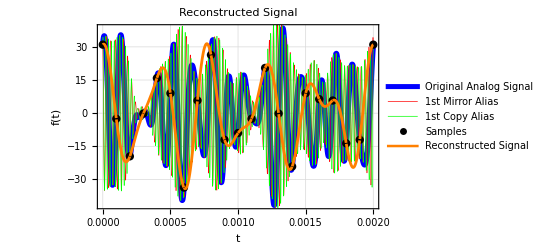

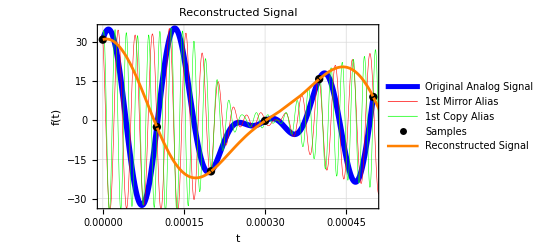

```mathematica
(* Define the set of shape functions. *)
ShapeFunctionSet2 = N[Table[Sin[2π*(SamplingFrequency2/2)*(t-n/SamplingFrequency2)] / (2π*(SamplingFrequency2/2)*(t-n/SamplingFrequency2)),
	{n, 0, Length[SamplingTime2]-1}]];
Print[Style["The set of shape functions: ", Bold, FontFamily->"Times", FontSize->14]]
TraditionalForm[ShapeFunctionSet]

(* Reconstruct the signal using the samples. *)
ReconstructedSignal2 = Dot[fSeq2, ShapeFunctionSet2];
Print[Style["The reconstructed signal using samples: ", Bold, FontFamily->"Times", FontSize->14]]
TraditionalForm[ReconstructedSignal2]

(* Plot the reconstructed signal with the original signal and its alias. *)
Show[Plot[f[t], {t, 0, 0.002}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.01]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Reconstructed Signal",
	GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
Plot[fMirror[t], {t, 0, 0.002}, PlotStyle->{Red, Thickness[0.001]},
	PlotLegends->{Style["1st Mirror Alias", Bold, FontSize->14, FontFamily->"Times"]}],
Plot[fCopy[t], {t, 0, 0.002}, PlotStyle->{Green, Thickness[0.001]},
	PlotLegends->{Style["1st Copy Alias", Bold, FontSize->14, FontFamily->"Times"]}],
ListPlot[fSeqList2, PlotStyle->{Directive[PointSize[0.015], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}],
Plot[ReconstructedSignal2, {t, 0, 0.002}, PlotStyle->{Orange, Thickness[0.005]},
	PlotLegends->{Style["Reconstructed Signal", Bold, FontSize->14, FontFamily->"Times"]}]]

Show[Plot[f[t], {t, 0, 0.0005}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.01]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Reconstructed Signal",
	GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
Plot[fMirror[t], {t, 0, 0.002}, PlotStyle->{Red, Thickness[0.001]},
	PlotLegends->{Style["1st Mirror Alias", Bold, FontSize->14, FontFamily->"Times"]}],
Plot[fCopy[t], {t, 0, 0.002}, PlotStyle->{Green, Thickness[0.001]},
	PlotLegends->{Style["1st Copy Alias", Bold, FontSize->14, FontFamily->"Times"]}],
ListPlot[fSeqList2, PlotStyle->{Directive[PointSize[0.015], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}],
Plot[ReconstructedSignal2, {t, 0, 0.002}, PlotStyle->{Orange, Thickness[0.005]},
	PlotLegends->{Style["Reconstructed Signal", Bold, FontSize->14, FontFamily->"Times"]}]]
```

The reconstructed signal does not match the original analog signal since the sampling frequency is lower than the Nyquist frequency of the signal. The sampling frequency is 10000 Hz for this case, which means that the maximum frequency that the reconstructed signal can capture is 5000 Hz (half of the sampling frequency). So all the components with frequency higher than 5000 Hz (6000 Hz, 7500 Hz and 10000 Hz) are missed.

## Problem 14

Samples after quantization by rounding:

{31,27,-12,-32,-3,33,24,-8,-20,-8,-1,-2,0,0,-5,0,16,12,-14,-21,9,31,6,-33,-34,-2,20,18,6,-10,-19,-4,26,28,-7,-31,-12,15,8,-13,-9,11,16,5,-3,-4,-4,7,20,7,-29,-39,0,37,23,-15,-24,-3,14,16,9,-6,-22,-18,6,13,-8,-19,6,27,9,-19,-14,13,21,6,-12,-22,-20,2,31}

Samples after quantization by truncating:

{31,26,-13,-33,-3,32,24,-9,-20,-8,-1,-3,-1,-1,-6,0,15,12,-15,-22,9,31,6,-33,-34,-2,20,18,5,-11,-20,-4,26,28,-8,-32,-13,14,7,-14,-9,11,16,4,-3,-5,-4,6,20,7,-30,-39,-1,36,23,-15,-25,-4,14,15,9,-6,-23,-18,6,13,-9,-19,5,26,9,-19,-14,13,21,5,-13,-23,-21,2,31}

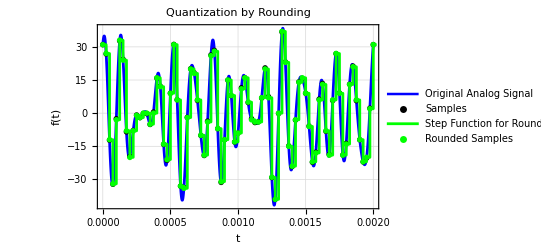

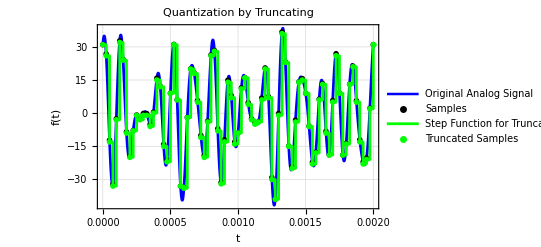

```mathematica
(* Quantization by rounding. *)
Print[Style["Samples after quantization by rounding: ", Bold, FontFamily->"Times", FontSize->14]]
fSeqRound = Round[fSeq, 1]
fSeqRoundList = Transpose[{SamplingTime, fSeqRound}];

(* Quantization by truncating. *)
Print[Style["Samples after quantization by truncating: ", Bold, FontFamily->"Times", FontSize->14]]
fSeqTruncate = Floor[fSeq, 1]
fSeqTruncateList = Transpose[{SamplingTime, fSeqTruncate}];

(* Plot the original signal and the rounded samples. *)
Show[Plot[f[t], {t, 0, 0.002}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.005]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Quantization by Rounding",
	GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
ListPlot[fSeqList, PlotStyle->{Directive[PointSize[0.01], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}],
ListStepPlot[fSeqRoundList, DataRange->{0, Length[fSeqRound]-1}, PlotStyle -> {Directive[PointSize[0.005], Green]},
	PlotLegends->{Style["Step Function for Rounded Samples", Bold, FontSize->14, FontFamily->"Times"]}],
ListPlot[fSeqRoundList, PlotStyle->{Directive[PointSize[0.01], Green]}, PlotLegends->{Style["Rounded Samples",
	Bold, FontSize->14, FontFamily->"Times"]}]]
	
(* Plot the original signal and the truncated samples. *)
Show[Plot[f[t], {t, 0, 0.002}, ImageSize->{400, 300}, PlotStyle->{Blue, Thickness[0.005]},
	PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},
	FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Quantization by Truncating",
	GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
ListPlot[fSeqList, PlotStyle->{Directive[PointSize[0.01], Black]}, PlotLegends->{Style["Samples",
	Bold, FontSize->14, FontFamily->"Times"]}],
ListStepPlot[fSeqTruncateList, DataRange->{0, Length[fSeqRound]-1}, PlotStyle -> {Directive[PointSize[0.005], Green]},
	PlotLegends->{Style["Step Function for Truncated Samples", Bold, FontSize->14, FontFamily->"Times"]}],
ListPlot[fSeqTruncateList, PlotStyle->{Directive[PointSize[0.01], Green]}, PlotLegends->{Style["Truncated Samples",
	Bold, FontSize->14, FontFamily->"Times"]}]]
```

## Problem 15

```mathematica
(* Calculate the average sampled sequence power. *)
Print[Style["Average sampled sequence power: ", Bold, FontFamily->"Times", FontSize->14]]
AvgSeqPower = Dot[fSeq, fSeq] / Length[fSeq]

(* Error calculation for rounding. *)
Print[Style["Error sequence for rounded samples: ", Bold, FontFamily->"Times", FontSize->14]]
RoundingError = fSeq - fSeqRound

Print[Style["Quantization error power for rounded samples: ", Bold, FontFamily->"Times", FontSize->14]]
RoundingErrorPower = Dot[RoundingError, RoundingError] / Length[RoundingError]

Print[Style["Signal-to-Noise ratio for rounded samples: ", Bold, FontFamily->"Times", FontSize->14]]
RoundingSNR = 10log[AvgSeqPower/RoundingErrorPower]

(* Error calculation for truncating. *)
Print[Style["Error sequence for truncated samples: ", Bold, FontFamily->"Times", FontSize->14]]
TruncatingError = fSeq - fSeqTruncate

Print[Style["Quantization error power for truncated samples: ", Bold, FontFamily->"Times", FontSize->14]]
TruncatingErrorPower = Dot[TruncatingError, TruncatingError] / Length[TruncatingError]

Print[Style["Signal-to-Noise ratio for truncated samples: ", Bold, FontFamily->"Times", FontSize->14]]
TruncatingSNR = 10log[AvgSeqPower/TruncatingErrorPower]
```

Average sampled sequence power:

321.

Error sequence for rounded samples:

{0.,-0.210838,-0.236164,-0.158708,0.47413,-0.279769,0.365176,-0.471285,0.460261,0.169881,0.142136,-0.011729,-0.157773,-0.203188,-0.094666,0.482096,-0.143904,0.190539,-0.138277,-0.317474,0.,0.0978023,0.0558242,0.00631796,0.34553,0.103691,0.0994353,0.316338,-0.279921,-0.056845,-0.142136,0.387283,0.338113,0.400397,-0.0092654,-0.306018,-0.0364355,-0.0804097,-0.0420628,-0.0580803,0.,0.481825,0.0481072,-0.203526,0.47413,-0.23495,0.0809045,-0.163948,0.460261,0.477218,-0.142136,0.0330897,-0.157773,-0.248007,0.189605,0.174758,-0.143904,-0.116799,0.145994,-0.362293,0.,0.142621,-0.228447,0.313655,0.34553,0.411028,-0.184836,0.361156,-0.279921,-0.101664,0.142136,0.0799459,0.338113,0.0930593,0.275006,-0.350836,-0.0364355,-0.035591,-0.326334,0.249257,0.}

Quantization error power for rounded samples:

0.0621903

Signal-to-Noise ratio for rounded samples:

10 log[5161.58]

Error sequence for truncated samples:

{0.,0.789162,0.763836,0.841292,0.47413,0.720231,0.365176,0.528715,0.460261,0.169881,0.142136,0.988271,0.842227,0.796812,0.905334,0.482096,0.856096,0.190539,0.861723,0.682526,0.,0.0978023,0.0558242,0.00631796,0.34553,0.103691,0.0994353,0.316338,0.720079,0.943155,0.857864,0.387283,0.338113,0.400397,0.990735,0.693982,0.963564,0.91959,0.957937,0.94192,0.,0.481825,0.0481072,0.796474,0.47413,0.76505,0.0809045,0.836052,0.460261,0.477218,0.857864,0.0330897,0.842227,0.751993,0.189605,0.174758,0.856096,0.883201,0.145994,0.637707,0.,0.142621,0.771553,0.313655,0.34553,0.411028,0.815164,0.361156,0.720079,0.898336,0.142136,0.0799459,0.338113,0.0930593,0.275006,0.649164,0.963564,0.964409,0.673666,0.249257,0.}

Quantization error power for truncated samples:

0.364601

Signal-to-Noise ratio for truncated samples:

10 log[880.413]